```mathematica
SelectClassData[data_,classcol_, class_, firstrow_,lastrow_, obj_] := List[#[[3]]/60000, #[[4]]]&/@ Select[Take[data,{firstrow,Min[Length[data],lastrow]}], #1[[classcol]] == class && #1[[4]] < obj &];
```

```mathematica
SetDirectory["E:\\Misceleniouse\\2008\\Master Thesis, RISC\\Project\\ProductionPlanning\\problem1\\Output\\Run70\\"]; 
DataSet=ImportString[Import["log.csv", "Text"],"CSV"];
```

```mathematica
IterData = SelectClassData[DataSet, 2, " iter", 1, 100000, 1000];
GraspData = SelectClassData[DataSet, 2, " grasp", 1, 100000, 1000];
Length[IterData]
Length[GraspData]
```

984

8

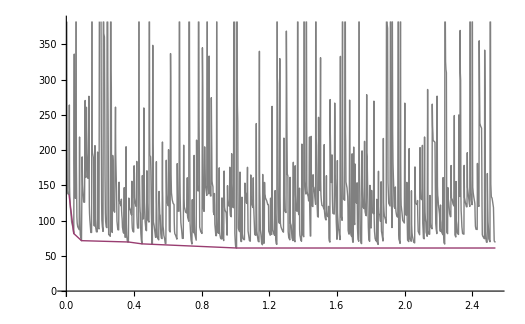

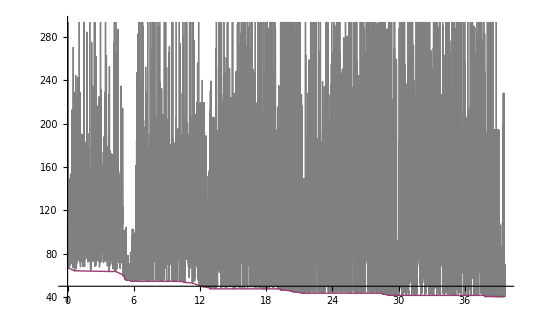

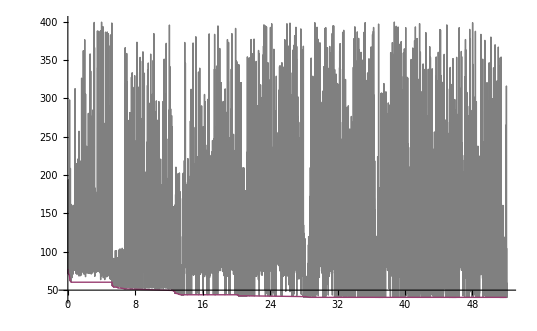

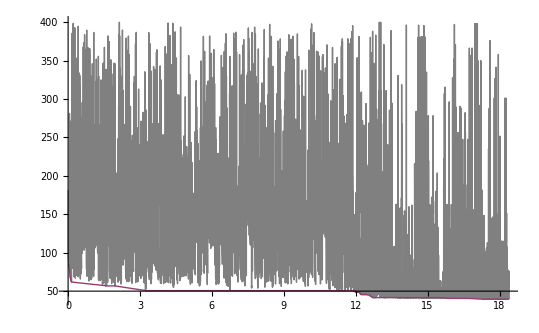

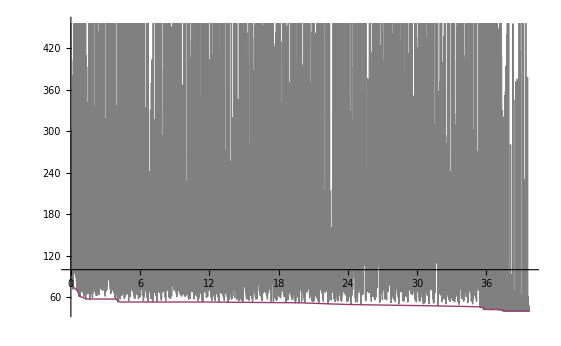

```mathematica
ListLinePlot[{IterData, GraspData, {{0, 0}}}, PlotStyle->{Gray, Thick}]
```